# MA2330

## 5.6 Discrete Dynamical Systems: x_(k+1)=A x_k

Our car problem is an example of a discrete dynamical system.  
	x_(k+1)=(0.9 | 0.1 | 0.3 | 0.2
0.1 | 0.8 | 0 | 0
0 | 0.1 | 0.7 | 0
0 | 0 | 0 | 0.8) x_k  	
The matrix A says where the cars rented from the North South East and West locations are returned to each day.

Biological problems produce similar systems.  An age-stage biological model splits a population by age:

The first entry of x is the population less than one.

The second entry of x is the population between one and two.

The p^th entry of x is the number between p and p+1.

Suppose the biological population is people. How does this vector change from year to year?  If the age stages are by year how long do our vectors need to be?

Discrete control theory problems add a control vector u_k to get the dynamical system 
	x_(k+1)=A x_k+u_k
The goal is to choose u_k to steer the system to some desired state.  The wiki page is probably too much
	https://en.wikipedia.org/wiki/Control_theory
 Any engineering school has a bunch of control theory courses which use a LOT of Linear Algebra
	 https://www.mtu.edu/gradschool/programs/certificates/control-systems/

We know how to write down the solution of
	x_(k+1)=A x_k  with initial condition x_0∈ℝ^n given
Assume A is diagonalizable, then we have eigenvectors v_1,v_2,…,v_n which span ℝ^n so 
	x_0=c_1 v_1+c_2 v_2+…+c_n v_n
so since A v_i=λ_i v_i we have 
	x_1 | = | A x_0 | = | c_1 A v_1+c_2 A v_2+…+c_n A v_n      
  |   |   |   | c_1 λ_1 v_1+c_2 λ_2 v_2+…+c_n λ_n v_n
as a result
	x_k | = | (c_1(λ_1))^k v_1+(c_2(λ_2))^k v_2+…+(c_n(λ_n))^k v_n
Eigenvalues are usually sorted big to little i.e. |λ_i|≥|λ_(i+1)|.  Assume this is the case and that the first inequality is actually|λ_1| >|λ_2| then 
	  x_k | = | (c_1(λ_1))^k v_1+(c_2(λ_2))^k v_2+…+(c_n(λ_n))^k v_n
x_k | = |  (λ_1)^k(c_1 v_1+(c_2(λ_2/λ_1))^k v_2+…+(c_n(λ_n/λ_1))^k v_n)
x_k | ≈ | (λ_1)^k c_1 v_1                                                                         
In words, the eigenvector associated with an isolated dominant eigenvalue determines the long time behavior.  If the dominant eigenvalue is greater than one in magnitude the solution grows exponentially. If the dominant eigenvalue is less than one in magnitude the solution decays exponentially.

### Pictures of Dynamical Systems

It is pretty easy to plot solutions of Dynamical Systems in 2 or 3 dimensions.

```mathematica
DySysPlot2D[A_]:= Module[
{x,Data, maxSteps=23,Δθ=π/11},
Data=Table[ 
x[0]={Cos[θ],Sin[θ]};
x[k_]:=A.x[k-1];
Table[x[k],{k,0,maxSteps}],
{θ,Δθ,2π,Δθ}];
ListPlot[Data,AspectRatio->Automatic,
Prolog->{Green, Circle[{0,0},1]},
Epilog->{Black,Arrowheads[Small],Thin,Map[Arrow,Data]},
PlotLabel->A]
]
```

```mathematica
DySysPlot2D[A_]:= Module[
{x,Data, maxSteps=23,Δθ=π/11},
Data=Table[ 
x[0]={Cos[θ],Sin[θ]};
x[k_]:=A.x[k-1];
Table[x[k],{k,0,maxSteps}],
{θ,Δθ,2π,Δθ}];
ListPlot[Data,AspectRatio->Automatic,
Prolog->{Green, Circle[{0,0},1]},
Epilog->{Black,Arrowheads[Small],Thin,Map[Arrow,Data]},
PlotLabel->A]
]
```

```mathematica
DySysPlot3D[A_]:= Module[
{x,Data, maxSteps=23,Δθ=π/6},
Data=Flatten[Table[ 
x[0]={Cos[θ]Sin[ϕ],Sin[θ]Sin[ϕ],Cos[ϕ]};
x[k_]:=A.x[k-1];
Table[x[k],{k,0,maxSteps}],
{ϕ,Δθ,π-Δθ,Δθ},{θ,Δθ,2π,Δθ}],1];
Show[
Graphics3D[{Opacity[0.2],LightGreen,Sphere[{0,0,0},1]}],
ListLinePlot3D[Data,BoxRatios->Automatic,
PlotMarkers->{"Point",Small},
PlotStyle->Thin,
PlotLabel->A]
]]
```

```mathematica
A=({{0.5, 0.4, 0}, {-0.104, 1.1, 0}, {0.1, 0, 0.9}});
DySysPlot3D[A]
```

-Graphics3D-

```mathematica
A=({{0.5, 0.4}, {-0.104, 1.1}});
DySysPlot2D[A]
```

-Graphics-

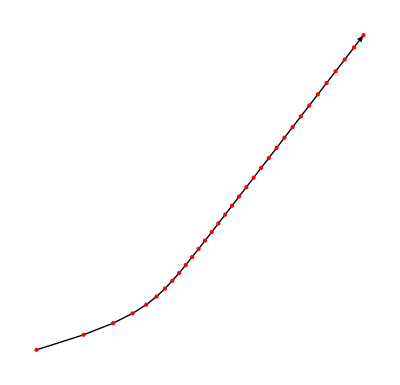

```mathematica
A=({{0.5, 0.4}, {-0.104, 1.1}});
x[k_]:=A.x[k-1]
x[0]={0.1,0.2};
maxStep=32;
Data=Table[x[k],{k,0, maxStep}];
Graphics[{Arrow[Data], Red,Point[Data]}]
```

## Row Op Code

```mathematica
Clear[RowScale,RowSwitch,RowAdd]
RowScale[A_,{i_, α_}]:=Module[{ANew=A,s},
s=Table[StringForm["row_(``)",k],{k, Length[A]}];
ANew⟦i,All⟧=α ANew⟦i,All⟧;
s⟦i⟧=StringForm["row_(``)→(``)row_(``)",i,α,i];
Print[MatrixForm[ANew],TableForm[s]];
ANew]
RowSwitch[A_,{i_,j_}]:=Module[{ANew=A,s},
s=Table[StringForm["row_(``)",k],{k, Length[A]}];
s⟦i⟧=StringForm["row_(``)→row_(``)",i,j];
s⟦j⟧=StringForm["row_(``)→row_(``)",j,i];
ANew⟦{i,j},All⟧=ANew⟦{j,i},All⟧;
Print[MatrixForm[ANew],TableForm[s]];
ANew]
RowAdd[A_,{i_,α_,p_}]:=Module[{ANew=A,s},
s=Table[StringForm["row_(``)",k],{k, Length[A]}];
s⟦i⟧=StringForm["row_(``)→ row_(``)+((``row)_(``))",i,i,α, p];
ANew⟦i,All⟧=ANew⟦i,All⟧+ α ANew⟦p,All⟧;
Print[MatrixForm[ANew],TableForm[s]];
ANew]
Clear[RowAdd]
RowAdd[A_,{iαs_,p_}]:=Module[{ANew=A,s,i,α},
s=Table[StringForm["row_(``)",k],{k, Length[A]}];
Do[
{i,α}=iαs⟦j⟧;
s⟦i⟧=StringForm["row_(``)→ row_(``)+((``row)_(``))",i,i,α, p];
ANew⟦i,All⟧=ANew⟦i,All⟧+ α ANew⟦p,All⟧,
{j,Length[iαs]}];
ANew=Simplify[ANew];
Print[MatrixForm[ANew],TableForm[s]];
ANew]
```